#### Problem description

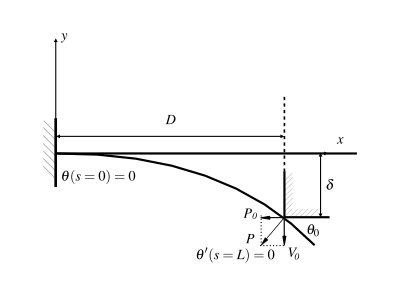

The governing equation for the Euler Elastica problem is

E I (d^2 θ)/(d t^2)-P_1 sin(θ)+ P_2 cos(θ)=0

where 0≤t≤S/2 is the arc length coordinate, θ is the angle of deflection (in radians) at point t, P_1 (positive when pointing to right) and P_2 (positive when pointing downward) are the horizontal and vertical forces at the left end of the beam, respectively.

Let ξ=t/(S/2), then the equation becomes

(4E I)/S^2 (d^2 θ)/dξ^2-P_1 sin(θ)+ P_2 cos(θ)=0

Note that

P_1=P_n sin(θ_0)-μ P_n cos(θ_0)
-P_2=P_n cos(θ_0)+μ P_n sin(θ_0)

P_1=P_n sin(θ_0)-μ P_n cos(θ_0)=P_n( sin(θ_0)-μ cos(θ_0))
P_2=-(P_n cos(θ_0)+μ P_n sin(θ_0))=-P_n(cos(θ_0)+μ sin(θ_0))

where θ_0=θ(ξ=0)>0, P_n>0 is the magnitude of the reaction force. Thus

(4E I)/(P_n S^2) (d^2 θ)/(d ξ^2)-( sin(θ_0)-μ cos(θ_0))sin(θ)- (cos(θ_0)+μ sin(θ_0))cos(θ)=0
 (d^2 θ)/dξ^2-(P_n S^2)/(4E I) (cos(θ_0-θ)+μ sin(θ_0-θ))=0
 (d^2 θ)/dξ^2-(P_n S^2)/(4E I) (cos(θ-θ_0)-μ sin(θ-θ_0))=0

Let k=(P_n S^2)/(4E I), g=θ-θ_0. Note that

g(ξ=0)=θ(ξ=0)-θ_0=0
g(ξ=1)=θ(ξ=1)-θ_0=-θ_0
g'(ξ=0)=θ'(ξ=0)=0

The simplified governing equation and boundary conditions are as follows

(d^2 g)/dξ^2-k (cos(g)-μ sin(g))=0
g(0)=0
g'(0)=0
g(1)=-θ_0

It seems like that the sign of θ is flipped. Because we are working in a Left-hand cartesian coordinate system.

θ_0=-(-g(1))
θ=-(g-g(1))
L=S∫_0^1 cos(θ(ξ)) dξ
w_0=S/2∫_0^1 sin(θ(ξ)) dξ
(P_n L^2)/(4E I)=(P_n S^2)/(4E I)(L/S)^2=k (L/S)^2=(k(∫_0^1 cos(θ) dξ))^2
(2 w_0)/L=(∫_0^1 sin(θ) dξ)/(∫_0^1 cos(θ) dξ)

### Force-deflection relations

θ_0=-(-g(1))
θ=-(g-g(1))
(P_n L^2)/(4E I)=(k(∫_0^1 cos(θ) dξ))^2
-P_2=P_n cos(θ_0)+μ P_n sin(θ_0)
F=-2 P_2=2(P_n cos(θ_0)+μ P_n sin(θ_0))
F=2P_n( cos(θ_0)+μ sin(θ_0))
(F L^2)/(4E I)=(P_n L^2)/(4E I)F/P_n=(P_n L^2)/(4E I)2( cos(θ_0)+μ sin(θ_0))
(F L^2)/(4E I)=2(k(∫_0^1 cos(θ) dξ))^2( cos(θ_0)+μ sin(θ_0))
(F L^2)/(E I)=8(k(∫_0^1 cos(θ) dξ))^2( cos(θ_0)+μ sin(θ_0))
F̂=(F L^2)/(E I)=8(k(∫_0^1 cos(θ) dξ))^2( cos(θ_0)+μ sin(θ_0))
OverHat[w_0]=w_0/L=(∫_0^1 sin(θ) dξ)/(2∫_0^1 cos(θ) dξ)

### Solution Vector = {OverHat[w_0], F̂, k}

```mathematica
μlist=Range[0,1,0.2];
```

```mathematica
SolutionVector=Table[ParallelTable[solg=NDSolve[{g''[ξ]-k( Cos[g[ξ]]-μ Sin[g[ξ]])==0,g[0]==0,g'[0]==0},g,{ξ,0,1}];
θ[ξ_]=-(g[ξ]-g[1])/.solg[[1]];
θ0=g[ξ]/.solg[[1]]/.ξ->1;
IntSinθ=NIntegrate[Sin[θ[ξ]],{ξ,0,1}];
IntCosθ=NIntegrate[Cos[θ[ξ]],{ξ,0,1}];
w=IntSinθ/(2IntCosθ);
F=8k IntCosθ^2( Cos[θ0]+μ  Sin[θ0]);
{w,F,k,θ0},{k,0.02,(μ+0.2)*20,0.02}],{μ,μlist}];
```

$Aborted

```mathematica
MaxF=Position[#,Max[#]][[1]]&/@SolutionVector[[;;,;;,2]];
Isp=MapIndexed[Part[SolutionVector,#2,#1[[1]]][[1]]&,MaxF]
```

{{0.238705,6.67178,1.36,0.669755},{0.268472,8.0167,1.56,0.745469},{0.294013,9.64187,1.76,0.810446},{0.223212,28.0987,16.,1.6859},{-0.151328,127.825,20.,0.809109},{-0.134386,140.61,17.78,0.698569}}

```mathematica
ShortSolVect[[;;,-1,3]]
```

{3.44,3.64,3.96,4.36,5.,7.}

```mathematica
Num =Length@μlist;
colorlist =ColorData["Rainbow"]/@((Range@Num-1)/(Num-1))
Stylelist=Directive[Thickness[0.008],#]&/@colorlist;
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.857359, 0.131106, 0.132128]}

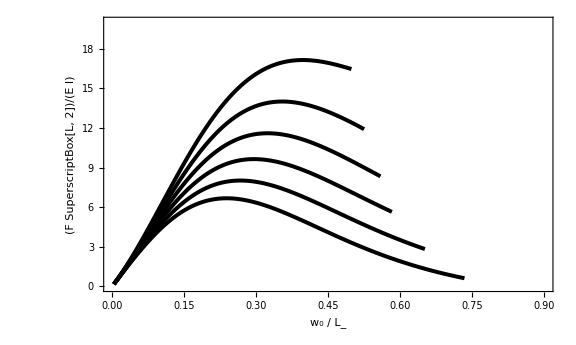

```mathematica
ShortSolVect={
SolutionVector[[1]][[;;160]],
SolutionVector[[2]][[;;160]],
SolutionVector[[3]][[;;160]],
SolutionVector[[4]][[;;170]],
SolutionVector[[5]][[;;180]],
SolutionVector[[6]][[;;200]]
};
p1=ListPlot[ShortSolVect[[;;,;;,1;;2]],Joined->True,PlotStyle->Directive[Black,Thickness[0.005]],ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
(*MaxF=Position[#,Max[#]][[1]]&/@ShortSolVect[[;;,;;,2]];
Isp=MapIndexed[Part[ShortSolVect,#2,#1[[1]]][[1]]&,MaxF]
pIsp=Graphics[{PointSize[Medium],Black,Point[Isp[[;;,1;;2]]]}];*)
(*pp2 =Table[Plot[48kc(ws-w0)/.kc->0.2/4,{w0,0,0.8},PlotStyle->{Black,Dashed}] ,{ws,2,5,0.05}];*)
(*p3=Show[p1,pp2]*)
```

```mathematica
ShortSolVect[[1,;;,1;;2]][[-1]]
```

{0.733633,0.60794}

```mathematica
ClearAll[n,data1,k,x,basis,f1,obliqueL1,psol1,TangentP,wsSol,ws]
```

```mathematica
basis=x^#&/@Range[0,10]
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}

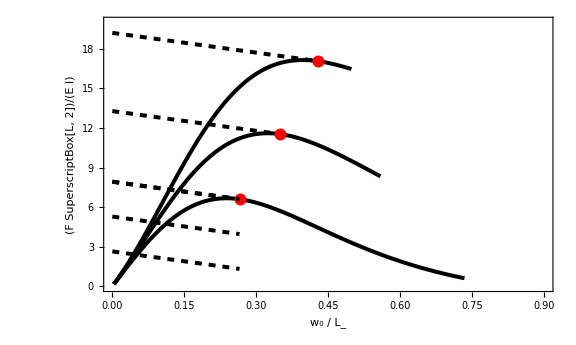

```mathematica
Pframe=Show@Table[
Module[{nlist=n,data1,k = 5,x,x2,basis,f1,obliqueL1,psol1,TangentP,wsSol,ws,PwCurve,ObliqueLine ,TangentPoint},
data1=ShortSolVect[[nlist,;;,1;;2]];
x2=data1[[-1,1]];
f1[x_]=Fit[data1,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
obliqueL1[w0_,ws_]=k(ws-w0);
psol1=NSolve[{f1'[x]==-k,0<x<x2},x,Reals];
TangentP={x/.psol1[[1]],f1[x/.psol1[[1]]]};
wsSol=NSolve[obliqueL1[TangentP[[1]],ws]==TangentP[[2]],ws];
PwCurve=ListPlot[data1,Joined->True,PlotStyle->Directive[Black,Thickness[0.005]],ImageSize->Large,
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6];
ObliqueLine=Plot[{obliqueL1[x,ws/.wsSol[[1]]]}, {x, 0, TangentP[[1]]}
,PlotStyle->Directive[Dashed,Black,Thickness[0.005]]];
TangentPoint=Graphics[{PointSize[0.015],Red,Point[TangentP]}];
Show[PwCurve,ObliqueLine ,TangentPoint,PlotRange->{{0.0,0.9},{0,20}}]]
,{n,{1,4,6}}];
PExtraOL=Module[{nlist=1,data1,k = 5,x,x2,basis,f1,obliqueL1,psol1,TangentP,wsSol,ws,ObliqueLine ,dis,nOL=3},
data1=ShortSolVect[[nlist,;;,1;;2]];
x2=data1[[-1,1]];
f1[x_]=Fit[data1,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
obliqueL1[w0_,ws_]=k(ws-w0);
psol1=NSolve[{f1'[x]==-k,0<x<x2},x,Reals];
TangentP={x/.psol1[[1]],f1[x/.psol1[[1]]]};
wsSol=NSolve[obliqueL1[TangentP[[1]],ws]==TangentP[[2]],ws];
dis=(ws/.wsSol[[1]])/nOL;
ObliqueLine=Plot[obliqueL1[x,#*dis]&/@Range@nOL, {x, 0, TangentP[[1]]}
,PlotStyle->Directive[(*Dashing[{0.015,0.02}]*)Dashed,Black,Thickness[0.005]]]];
Pschematic1=Show[Pframe,PExtraOL]
```

```mathematica
Export["FwFriction_V4.eps",Pschematic1]
```

FwFriction_V4.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["FwFriction_V3.eps"]]]
```

{{0.238705,6.67178,1.36,0.669755},{0.268472,8.0167,1.56,0.745469},{0.294013,9.64187,1.76,0.810446},{0.324018,11.6022,2.02,0.88603},{0.353927,14.0088,2.34,0.96325},{0.527223,19.555,7.,1.56564}}

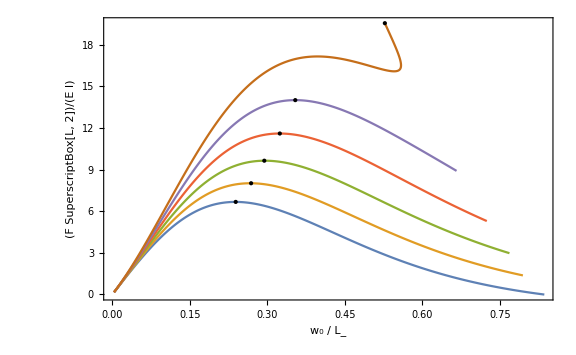

```mathematica
ShortSolVect={
SolutionVector[[1]][[;;172]],
SolutionVector[[2]][[;;182]],
SolutionVector[[3]][[;;198]],
SolutionVector[[4]][[;;218]],
SolutionVector[[5]][[;;250]],
SolutionVector[[6]][[;;350]]
};
p1=ListPlot[ShortSolVect[[;;,;;,1;;2]],Joined->True,PlotStyle->colorlist(*Directive[Red,Thickness[0.004],Dashed]*),ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->Automatic,
AxesStyle->Directive[Black,FontFamily->"Times",28],Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",16],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",16],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False];
MaxF=Position[#,Max[#]][[1]]&/@ShortSolVect[[;;,;;,2]];
Isp=MapIndexed[Part[ShortSolVect,#2,#1[[1]]][[1]]&,MaxF]
pIsp=Graphics[{PointSize[Medium],Black,Point[Isp[[;;,1;;2]]]}];
p3=Show[p1,pIsp]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Personal)/Apps/ShareLaTeX/Stair Step Pattern 2018/Figures

```mathematica
Export["FwFriction.eps",p3]
```

FwFriction.eps

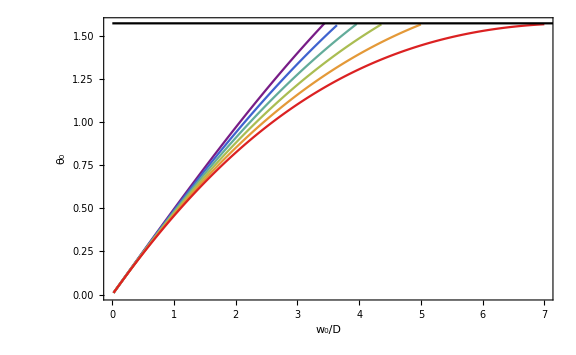

```mathematica
ShortSolVect={
SolutionVector[[1]][[;;172]],
SolutionVector[[2]][[;;182]],
SolutionVector[[3]][[;;198]],
SolutionVector[[4]][[;;218]],
SolutionVector[[5]][[;;250]],
SolutionVector[[6]][[;;350]]
};
p1=ListPlot[ShortSolVect[[;;,;;,{3,4}]],Joined->True,PlotStyle->colorlist(*Directive[Red,Thickness[0.004],Dashed]*),PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["w_0/D",Black,FontFamily->"Times",16],Style["θ_0",Black,FontFamily->"Times",16]},RotateLabel->False];
p2= Plot[π/2,{x,0,10},PlotStyle->Black];
Show[p1,p2]
```

```mathematica
ShortSolVect[[2,;;,4]]
```

{0.00999662,0.0199864,0.0299691,0.0399446,0.0499126,0.0598729,0.0698254,0.0797699,0.0897062,0.099634,0.109553,0.119464,0.129365,0.139257,0.14914,0.159014,0.168877,0.178731,0.188575,0.198408,0.208231,0.218043,0.227845,0.237635,0.247414,0.257182,0.266939,0.276683,0.286416,0.296137,0.305845,0.315541,0.325225,0.334896,0.344554,0.354198,0.36383,0.373448,0.383053,0.392644,0.402221,0.411784,0.421333,0.430867,0.440387,0.449892,0.459383,0.468858,0.478319,0.487764,0.497193,0.506608,0.516006,0.525389,0.534755,0.544106,0.55344,0.562758,0.572059,0.581344,0.590612,0.599863,0.609096,0.618313,0.627512,0.636694,0.645858,0.655005,0.664134,0.673244,0.682337,0.691411,0.700467,0.709505,0.718524,0.727525,0.736507,0.745469,0.754413,0.763338,0.772244,0.78113,0.789997,0.798844,0.807672,0.81648,0.825268,0.834036,0.842784,0.851513,0.860221,0.868908,0.877576,0.886223,0.894849,0.903455,0.91204,0.920604,0.929147,0.937669,0.946171,0.954651,0.96311,0.971548,0.979964,0.988359,0.996733,1.00508,1.01341,1.02172,1.03001,1.03828,1.04652,1.05474,1.06294,1.07112,1.07927,1.0874,1.09552,1.1036,1.11167,1.11971,1.12774,1.13573,1.14371,1.15166,1.1596,1.1675,1.17539,1.18325,1.19109,1.19891,1.2067,1.21448,1.22222,1.22995,1.23765,1.24533,1.25299,1.26062,1.26823,1.27582,1.28338,1.29093,1.29844,1.30594,1.31341,1.32086,1.32828,1.33568,1.34306,1.35041,1.35775,1.36505,1.37234,1.3796,1.38684,1.39405,1.40124,1.40841,1.41555,1.42267,1.42977,1.43684,1.44389,1.45092,1.45792,1.4649,1.47185,1.47879,1.4857,1.49258,1.49944,1.50628,1.51309,1.51989,1.52665,1.5334,1.54012,1.54681,1.55349,1.56014}

```mathematica
SetDirectory[NotebookDirectory[]];
Save["SolutionVector",SolutionVector]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SolutionVector3"];
```

Get::noopen: Cannot open SolutionVector3.

### Quantitative comparison

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
BendTests=Import["data/201708_BendTests_SS_processed_data.mat"];
```

```mathematica
Bendlabels=Import["data/201708_BendTests_SS_processed_data.mat","Labels"]
```

{Bstif,D,E,Fslp,Fstar,K_s,Kc_SE,Kcant,L,N_L,SSpattern,T_file,dSstar,sD,s_L,w0slp,w0star,w_sslp,w_sstar}

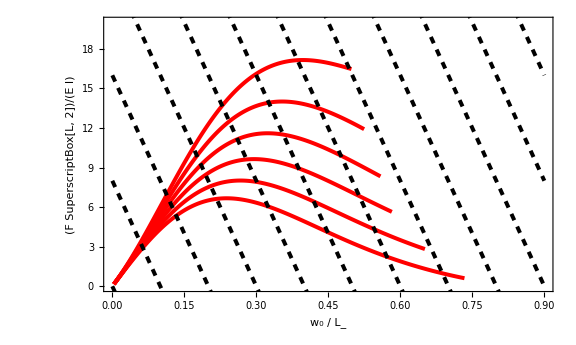

```mathematica
ShortSolVect={
SolutionVector[[1]][[;;160]],
SolutionVector[[2]][[;;160]],
SolutionVector[[3]][[;;160]],
SolutionVector[[4]][[;;170]],
SolutionVector[[5]][[;;180]],
SolutionVector[[6]][[;;200]]
};
p1=ListPlot[ShortSolVect[[;;,;;,1;;2]],Joined->True,PlotStyle->Directive[Red,Thickness[0.005]],ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6];
PExtraOL=Module[{nlist=1,data1,k =80,x,x2,basis,f1,obliqueL1,psol1,TangentP,wsSol,ws,ObliqueLine ,dis,nOL=3},
data1=ShortSolVect[[nlist,;;,1;;2]];
x2=data1[[-1,1]];
f1[x_]=Fit[data1,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
obliqueL1[w0_,ws_]=k(ws-w0);
(*psol1=NSolve[{f1'[x]==-k,0<x<x2},x,Reals];
TangentP={x/.psol1[[1]],f1[x/.psol1[[1]]]};
wsSol=NSolve[obliqueL1[TangentP[[1]],ws]==TangentP[[2]],ws];*)
(*dis=(ws/.wsSol[[1]])/nOL;*)
ObliqueLine=Plot[obliqueL1[x,#]&/@Range[-1,2,0.1], {x, 0, 0.9}
,PlotStyle->Directive[(*Dashing[{0.015,0.02}]*)Dashed,Black,Thickness[0.005]]]];
p3=Show[p1,PExtraOL]
```

```mathematica
Bstif=Flatten[ BendTests[[Position[Bendlabels,"Bstif"][[1,1]] ]]];
Kcant=Flatten[ BendTests[[Position[Bendlabels,"Kcant"][[1,1]] ]]];
w0slp=Flatten[ BendTests[[Position[Bendlabels,"w0slp"][[1,1]] ]]];
wsslp=Flatten[ BendTests[[Position[Bendlabels,"w_sslp"][[1,1]] ]]];
L=Flatten[ BendTests[[Position[Bendlabels,"L"][[1,1]] ]]];
SSpattern=Flatten[ BendTests[[Position[Bendlabels,"SSpattern"][[1,1]] ]]];
Fslp=Flatten[ BendTests[[Position[Bendlabels,"Fslp"][[1,1]] ]]];
Pslip=Flatten@Position[SSpattern,True];
deflection=(w0slp/L)[[Pslip]]
StageDis=(wsslp/L)[[Pslip]]
force=(Fslp*Bstif/L)[[Pslip]]
OblSlope=(Kcant/Bstif)[[Pslip]];
Max[OblSlope]
Min[OblSlope]
Max[StageDis]
Min[StageDis]
```

{0.168745,0.128139,0.205294,0.0312278,0.201919,0.211676,0.214201,0.125474,0.15329,0.110885,0.184022,0.171423,0.16935,0.163371,0.175034,0.205945,0.171424,0.176338,0.25857,0.166789,0.213613,0.197813,0.198963,0.183264,0.201468}

{0.26388,0.205807,0.406232,0.0549538,0.303361,0.364237,0.389421,0.18371,0.230895,0.149293,0.336059,0.238732,0.246529,0.193071,0.306131,0.400151,0.21036,0.312594,0.359653,0.278017,0.356372,0.304858,0.328514,0.296102,0.286517}

{9.70158,8.06689,45.5355,3.67405,8.42895,27.0818,25.8097,4.72903,7.18109,2.46605,22.9692,5.08439,6.55865,0.953481,17.3299,31.5404,1.91176,18.5264,11.8352,13.4431,18.8715,10.2194,14.2709,12.0252,5.7877}

255.94

36.2582

0.406232

0.0549538

```mathematica
SilpPoints=Point[Partition[Riffle[StageDis,force],2]]
```

Point[{{0.26388,9.70158},{0.205807,8.06689},{0.406232,45.5355},{0.0549538,3.67405},{0.303361,8.42895},{0.364237,27.0818},{0.389421,25.8097},{0.18371,4.72903},{0.230895,7.18109},{0.149293,2.46605},{0.336059,22.9692},{0.238732,5.08439},{0.246529,6.55865},{0.193071,0.953481},{0.306131,17.3299},{0.400151,31.5404},{0.21036,1.91176},{0.312594,18.5264},{0.359653,11.8352},{0.278017,13.4431},{0.356372,18.8715},{0.304858,10.2194},{0.328514,14.2709},{0.296102,12.0252},{0.286517,5.7877}}]

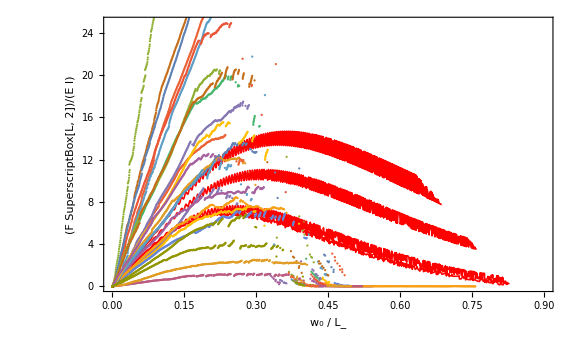

```mathematica
Psinu=Module[{μ0={0.0,0.1,0.5,0.8},A = 0.05,λ=0.001},
arclength=SolutionVector3[[;;,;;,5]];
frictionC=SolutionVector3[[;;,;;,6]];
levelset=frictionC-A Cos[arclength/λ];
data1=Flatten[Table[{SolutionVector3[[i,j,1]],SolutionVector3[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector3},{j,1,Length[SolutionVector3[[i]]]}],1];
	Level0p1=Table[Select[data1,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
(*Level0p4=Select[data1,Abs[#[[3]]-0.5]<10^-3&];
Level0p8=Select[data1,Abs[#[[3]]-0.8]<10^-3&];*)
Level0p1S=(SortBy[Level0p1[[#]],First])&/@Range@Length@μ0;
(*Level0p4S=SortBy[Level0p4,First];
Level0p8S=SortBy[Level0p8,First];*)
(*Level3={Level0p1S[[;;,{1,2}]],Level0p4S[[;;,{1,2}]],Level0p8S[[;;,{1,2}]]};*)
Level3=Level0p1S[[;;,;;,{1,2}]];
ListPlot[Level3,
Joined->True,
PlotStyle->Directive[Red,Thickness[0.002]],ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,25}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]];
p3=Show[Psinu,Pexp]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Personal)/Apps/ShareLaTeX/Stair Step Pattern 2018/Figures

```mathematica
BendTestAll=Import["data/201708_BendTests_SS_processed_data3.mat"];
```

```mathematica
BendlabelAll=Import["data/201708_BendTests_SS_processed_data3.mat","Labels"]
```

{Fslp,Fstar,dflctn,dsplcmnt,force}

```mathematica
force= BendTestAll[[Position[BendlabelAll,"force"][[1,1]] ]];
dflctn= BendTestAll[[Position[BendlabelAll,"dflctn"][[1,1]] ]];
```

```mathematica
fw0=Table[{dflctn[[i,j]]/L[[i]],force[[i,j]]*Bstif[[i]]/L[[i]]},{i,Pslip},{j,Length@force[[i]]}];
```

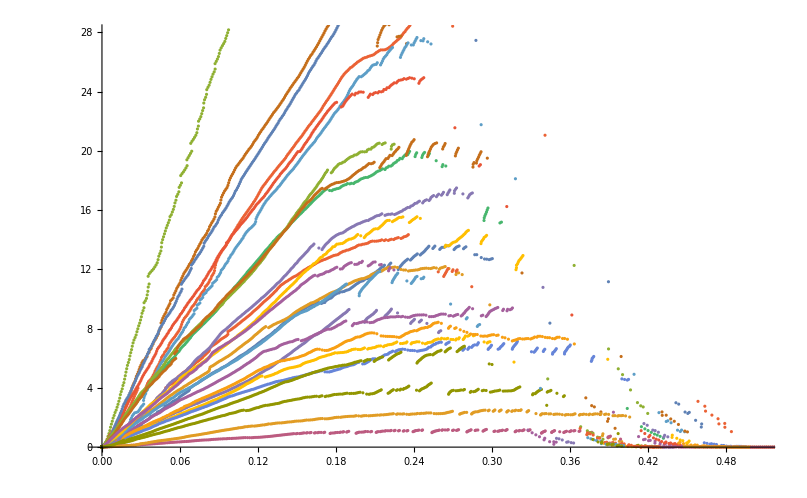

```mathematica
Pexp=ListPlot[fw0,]
```

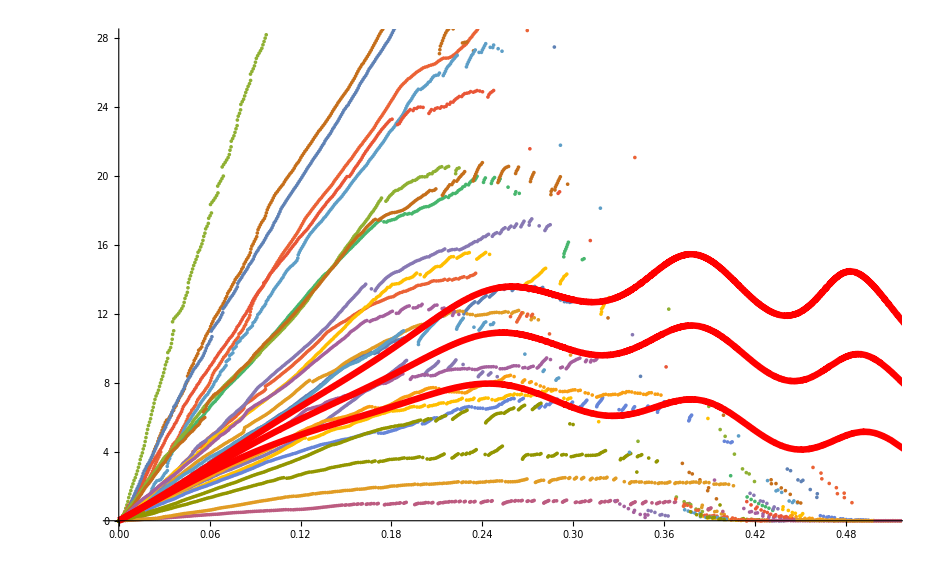

```mathematica
Module[{μ0={0.0,0.1,0.5,0.8},A = 0.05,λ=0.001},
arclength=SolutionVector3[[;;,;;,5]];
frictionC=SolutionVector3[[;;,;;,6]];
levelset=frictionC-A Cos[arclength/λ];
data1=Flatten[Table[{SolutionVector3[[i,j,1]],SolutionVector3[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector3},{j,1,Length[SolutionVector3[[i]]]}],1];
ListContourPlot[data1,
(*PlotStyle->colorlist(*Directive[Red,Thickness[0.004],Dashed]*),*)
ColorFunction->(ColorData[{"LightTemperatureMap","Reverse"}][#1]&),
PlotLegends->Automatic,
ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->Automatic,
AxesStyle->Directive[Black,FontFamily->"Times",28],Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",16],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",16],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False]
]
```